## -Graphics- -------> -Graphics- Сегментация изображения в wolfram alpha

```mathematica
WolframAlpha["2+2","SpokenResult"]
```

2 plus 2 is 4

```mathematica
WolframAlpha["2+2","ShortAnswer"]
```

4

```mathematica
WolframAlpha["caffeine",{{"3DStructure:ChemicalData",1},"Content"}]
```

-Graphics-

```mathematica
ListAnimate[Table[WolframAlpha[StringJoin["Koch snowflake, ",ToString[i]," iterations"],{{"KochSnowflake",1},"Content"}],{i,1,5}]]
```

```mathematica
WolframAlpha["weather"]
```

WolframAlphaQueryResults

```mathematica
WolframAlpha["area of countries"]
```

WolframAlphaQueryResults

```mathematica
countryAreaDataText=StringToStream[WolframAlpha["area of countries",{{"PropertyRanking:CountryData",1},"Plaintext"}]]
```

InputStream[…]

```mathematica
Find[countryAreaDataText,"Russia"]
```

1 | Russia | 1.71×10^7 km^2

```mathematica
countryAreaData=WolframAlpha["area of countries",{{"PropertyRanking:CountryData",1},"ComputableData"}]
```

{{1,Russia,1.71×10^7 km^2},{2,Canada,9.985×10^6 km^2},{3,United States,9.631×10^6 km^2},{4,China,9.597×10^6 km^2},{5,Brazil,8.515×10^6 km^2},{6,Australia,7.741×10^6 km^2},{7,India,3.287×10^6 km^2},{8,Argentina,2.767×10^6 km^2},{9,Kazakhstan,2.725×10^6 km^2},{10,Algeria,2.382×10^6 km^2},{11,Democratic Republic of the Congo,2.345×10^6 km^2},{12,Greenland,2.166×10^6 km^2},{13,Mexico,1.964×10^6 km^2},{14,Saudi Arabia,1.961×10^6 km^2},{15,Indonesia,1.905×10^6 km^2},{16,Sudan,1.886×10^6 km^2},{17,Libya,1.76×10^6 km^2},{18,Iran,1.648×10^6 km^2},{19,Mongolia,1.564×10^6 km^2},{20,Peru,1.285×10^6 km^2},{21,Chad,1.284×10^6 km^2},{22,Niger,1.267×10^6 km^2},{23,Angola,1.247×10^6 km^2},{24,Mali,1.24×10^6 km^2},{25,South Africa,1.219×10^6 km^2},{26,Colombia,1.139×10^6 km^2},{27,Ethiopia,1.127×10^6 km^2},{28,Bolivia,1.099×10^6 km^2},{29,Mauritania,1.031×10^6 km^2},{30,Egypt,1.001×10^6 km^2},{31,Tanzania,947300. km^2},{32,Nigeria,923800. km^2},{33,Venezuela,912100. km^2},{34,Namibia,824300. km^2},{35,Mozambique,799400. km^2},{36,Pakistan,796100. km^2},{37,Turkey,783600. km^2},{38,Chile,756100. km^2},{39,Zambia,752600. km^2},{40,Myanmar,676600. km^2},{41,Afghanistan,652200. km^2},{42,South Sudan,644300. km^2},{43,Somalia,637700. km^2},{44,Central African Republic,623000. km^2},{45,Ukraine,603600. km^2},{46,Madagascar,587000. km^2},{47,Botswana,581700. km^2},{48,Kenya,580400. km^2},{49,France,551500. km^2},{50,Yemen,528000. km^2},{51,Thailand,513100. km^2},{52,Spain,505400. km^2},{53,Turkmenistan,488100. km^2},{54,Cameroon,475400. km^2},{55,Papua New Guinea,462800. km^2},{56,Sweden,450300. km^2},{57,Uzbekistan,447400. km^2},{58,Morocco,446600. km^2},{59,French Southern And Antarctic lands,439800. km^2},{60,Iraq,437100. km^2},{61,Paraguay,406800. km^2},{62,Zimbabwe,390800. km^2},{63,Japan,377800. km^2},{64,Germany,357000. km^2},{65,Republic of the Congo,342000. km^2},{66,Finland,338100. km^2},{67,Malaysia,329800. km^2},{68,Vietnam,329600. km^2},{69,Norway,323800. km^2},{70,Ivory Coast,322500. km^2},{71,Poland,312700. km^2},{72,Oman,309500. km^2},{73,Italy,301300. km^2},{74,Philippines,300000. km^2},{75,Ecuador,283600. km^2},{76,Burkina Faso,274200. km^2},{77,New Zealand,268700. km^2},{78,Gabon,267700. km^2},{79,Western Sahara,266000. km^2},{80,Guinea,245900. km^2},{81,United Kingdom,243600. km^2},{82,Ghana,238500. km^2},{83,Romania,238400. km^2},{84,Laos,236800. km^2},{85,Uganda,236000. km^2},{86,Guyana,215000. km^2},{87,Belarus,207600. km^2},{88,Kyrgyzstan,200000. km^2},{89,Senegal,196700. km^2},{90,Syria,185200. km^2},{91,Cambodia,181000. km^2},{92,Uruguay,176200. km^2},{93,Suriname,163800. km^2},{94,Tunisia,163600. km^2},{95,Bangladesh,148500. km^2},{96,Nepal,147200. km^2},{97,Tajikistan,143100. km^2},{98,Greece,131900. km^2},{99,Nicaragua,130400. km^2},{100,North Korea,120500. km^2},{101,Malawi,118500. km^2},{102,Eritrea,117600. km^2},{103,Benin,112600. km^2},{104,Honduras,112100. km^2},{105,Liberia,111400. km^2},{106,Bulgaria,110900. km^2},{107,Cuba,110900. km^2},{108,Guatemala,108900. km^2},{109,Iceland,103000. km^2},{110,South Korea,98480. km^2},{111,Hungary,93030. km^2},{112,Portugal,92090. km^2},{113,French Guiana,91000. km^2},{114,Jordan,89340. km^2},{115,Azerbaijan,86600. km^2},{116,Austria,83870. km^2},{117,United Arab Emirates,83600. km^2},{118,Czech Republic,78870. km^2},{119,Serbia,77470. km^2},{120,Panama,75420. km^2},{121,Sierra Leone,71740. km^2},{122,Ireland,70270. km^2},{123,Georgia,69700. km^2},{124,Sri Lanka,65610. km^2},{125,Lithuania,65300. km^2},{126,Latvia,64590. km^2},{127,Svalbard,62050. km^2},{128,Togo,56790. km^2},{129,Croatia,56590. km^2},{130,British Indian Ocean Territory,54400. km^2},{131,Bosnia and Herzegovina,51200. km^2},{132,Costa Rica,51100. km^2},{133,Slovakia,49040. km^2},{134,Dominican Republic,48670. km^2},{135,Estonia,45230. km^2},{136,Denmark,43090. km^2},{137,Netherlands,41540. km^2},{138,Switzerland,41280. km^2},{139,Bhutan,38390. km^2},{140,Guinea-Bissau,36130. km^2},{141,Taiwan,35980. km^2},{142,Moldova,33850. km^2},{143,Belgium,30530. km^2},{144,Lesotho,30360. km^2},{145,Armenia,29740. km^2},{146,Solomon Islands,28900. km^2},{147,Albania,28750. km^2},{148,Equatorial Guinea,28050. km^2},{149,Burundi,27830. km^2},{150,Haiti,27750. km^2},{151,Rwanda,26340. km^2},{152,North Macedonia,25710. km^2},{153,Djibouti,23200. km^2},{154,Belize,22970. km^2},{155,El Salvador,21040. km^2},{156,Israel,20770. km^2},{157,Slovenia,20270. km^2},{158,New Caledonia,18580. km^2},{159,Fiji,18270. km^2},{160,Kuwait,17820. km^2},{161,Eswatini,17360. km^2},{162,East Timor,14870. km^2},{163,Bahamas,13880. km^2},{164,Montenegro,13810. km^2},{165,Vanuatu,12190. km^2},{166,Falkland Islands,12170. km^2},{167,Qatar,11590. km^2},{168,Gambia,11300. km^2},{169,Jamaica,10990. km^2},{170,Kosovo,10890. km^2},{171,Lebanon,10450. km^2},{172,Cyprus,9251. km^2},{173,Puerto Rico,9045. km^2},{174,West Bank,5860. km^2},{175,Brunei,5765. km^2},{176,Trinidad and Tobago,5128. km^2},{177,French Polynesia,4167. km^2},{178,Cape Verde,4033. km^2},{179,South Georgia and the South Sandwich Islands,3903. km^2},{180,Samoa,2831. km^2},{181,Luxembourg,2586. km^2},{182,Réunion,2517. km^2},{183,Comoros,2235. km^2},{184,Mauritius,2040. km^2},{185,Guadeloupe,1780. km^2},{186,Aland Islands,1580. km^2},{187,Faroe Islands,1393. km^2},{188,Hong Kong,1104. km^2},{189,Martinique,1100. km^2},{190,São Tomé and Príncipe,964. km^2},{191,Turks and Caicos Islands,948. km^2},{192,Kiribati,811. km^2},{193,Bahrain,760. km^2},{194,Dominica,751. km^2},{195,Tonga,747. km^2},{196,Micronesia,702. km^2},{197,Singapore,697. km^2},{198,Saint Lucia,616. km^2},{199,Isle of Man,572. km^2},{200,Guam,544. km^2},{201,Andorra,468. km^2},{202,Northern Mariana Islands,464. km^2},{203,Palau,459. km^2},{204,Seychelles,455. km^2},{205,Curacao,444. km^2},{206,Antigua and Barbuda,442.6 km^2},{207,Barbados,430. km^2},{208,Saint Helena, Ascension and Tristan da Cunha,413. km^2},{209,Saint Vincent and the Grenadines,389. km^2},{210,Mayotte,374. km^2},{211,Gaza Strip,360. km^2},{212,United States Virgin Islands,349. km^2},{213,Grenada,344. km^2},{214,Caribbean Netherlands,328. km^2},{215,Malta,316. km^2},{216,Maldives,298. km^2},{217,Cayman Islands,264. km^2},{218,Saint Kitts and Nevis,261. km^2},{219,Niue,260. km^2},{220,Saint Pierre and Miquelon,242. km^2},{221,Cook Islands,236. km^2},{222,American Samoa,199. km^2},{223,Marshall Islands,181. km^2},{224,Aruba,180. km^2},{225,Liechtenstein,160. km^2},{226,British Virgin Islands,151. km^2},{227,Wallis and Futuna Islands,142. km^2},{228,Christmas Island,135. km^2},{229,Jersey,116. km^2},{230,Montserrat,102. km^2},{231,Anguilla,91. km^2},{232,Guernsey,78. km^2},{233,San Marino,61. km^2},{234,Bermuda,54. km^2},{235,Saint Martin,53.2 km^2},{236,Bouvet Island,49. km^2},{237,Pitcairn Islands,47. km^2},{238,Norfolk Island,36. km^2},{239,United States Minor Outlying Islands,34.2 km^2},{240,Sint Maarten,34. km^2},{241,Macau,28.2 km^2},{242,Tuvalu,26. km^2},{243,Saint Barthelemy,25. km^2},{244,Nauru,21. km^2},{245,Cocos Keeling Islands,14. km^2},{246,Tokelau,12. km^2},{247,Gibraltar,6.5 km^2},{248,Monaco,2. km^2},{249,Vatican City,0.44 km^2}}

```mathematica
Select[countryAreaData,MemberQ[#,"Russia"]&]
```

{{1,Russia,1.71×10^7 km^2}}

```mathematica
Select[countryAreaData,StringContainsQ[#[[2]],"Islands"]&]
```

{{146,Solomon Islands,28900. km^2},{166,Falkland Islands,12170. km^2},{179,South Georgia and the South Sandwich Islands,3903. km^2},{186,Aland Islands,1580. km^2},{187,Faroe Islands,1393. km^2},{191,Turks and Caicos Islands,948. km^2},{202,Northern Mariana Islands,464. km^2},{212,United States Virgin Islands,349. km^2},{217,Cayman Islands,264. km^2},{221,Cook Islands,236. km^2},{223,Marshall Islands,181. km^2},{226,British Virgin Islands,151. km^2},{227,Wallis and Futuna Islands,142. km^2},{237,Pitcairn Islands,47. km^2},{239,United States Minor Outlying Islands,34.2 km^2},{245,Cocos Keeling Islands,14. km^2}}

```mathematica
Needs["DatabaseLink`"]
conn=OpenSQLConnection["demo"]
```

SQLConnection[…]

```mathematica
SQLCreateTable[conn,SQLTable["CountryArea"],
{SQLColumn["id","DataTypeName"->"INTEGER"],
SQLColumn["Title","DataTypeName"->"VARCHAR","DataLength"->255],
SQLColumn["Area","DataTypeName"->"DOUBLE"]}
]
```

```mathematica
Table[SQLExecute[conn,"INSERT INTO CountryArea (id,Title,Area) VALUES (`1`,`2`,`3`)",{countryAreaData[[i]][[1]],countryAreaData[[i]][[2]],countryAreaData[[i]][[3]][[1]]}],{i,249}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
SQLExecute[conn,"SELECT * FROM CountryArea"]
```

{{1,Russia,1.71×10^7},{2,Canada,9.985×10^6},{3,United States,9.631×10^6},{4,China,9.597×10^6},{5,Brazil,8.515×10^6},{6,Australia,7.741×10^6},{7,India,3.287×10^6},{8,Argentina,2.767×10^6},{9,Kazakhstan,2.725×10^6},{10,Algeria,2.382×10^6},{11,Democratic Republic of the Congo,2.345×10^6},{12,Greenland,2.166×10^6},{13,Mexico,1.964×10^6},{14,Saudi Arabia,1.961×10^6},{15,Indonesia,1.905×10^6},{16,Sudan,1.886×10^6},{17,Libya,1.76×10^6},{18,Iran,1.648×10^6},{19,Mongolia,1.564×10^6},{20,Peru,1.285×10^6},{21,Chad,1.284×10^6},{22,Niger,1.267×10^6},{23,Angola,1.247×10^6},{24,Mali,1.24×10^6},{25,South Africa,1.219×10^6},{26,Colombia,1.139×10^6},{27,Ethiopia,1.127×10^6},{28,Bolivia,1.099×10^6},{29,Mauritania,1.031×10^6},{30,Egypt,1.001×10^6},{31,Tanzania,947300.},{32,Nigeria,923800.},{33,Venezuela,912100.},{34,Namibia,824300.},{35,Mozambique,799400.},{36,Pakistan,796100.},{37,Turkey,783600.},{38,Chile,756100.},{39,Zambia,752600.},{40,Myanmar,676600.},{41,Afghanistan,652200.},{42,South Sudan,644300.},{43,Somalia,637700.},{44,Central African Republic,623000.},{45,Ukraine,603600.},{46,Madagascar,587000.},{47,Botswana,581700.},{48,Kenya,580400.},{49,France,551500.},{50,Yemen,528000.},{51,Thailand,513100.},{52,Spain,505400.},{53,Turkmenistan,488100.},{54,Cameroon,475400.},{55,Papua New Guinea,462800.},{56,Sweden,450300.},{57,Uzbekistan,447400.},{58,Morocco,446600.},{59,French Southern And Antarctic lands,439800.},{60,Iraq,437100.},{61,Paraguay,406800.},{62,Zimbabwe,390800.},{63,Japan,377800.},{64,Germany,357000.},{65,Republic of the Congo,342000.},{66,Finland,338100.},{67,Malaysia,329800.},{68,Vietnam,329600.},{69,Norway,323800.},{70,Ivory Coast,322500.},{71,Poland,312700.},{72,Oman,309500.},{73,Italy,301300.},{74,Philippines,300000.},{75,Ecuador,283600.},{76,Burkina Faso,274200.},{77,New Zealand,268700.},{78,Gabon,267700.},{79,Western Sahara,266000.},{80,Guinea,245900.},{81,United Kingdom,243600.},{82,Ghana,238500.},{83,Romania,238400.},{84,Laos,236800.},{85,Uganda,236000.},{86,Guyana,215000.},{87,Belarus,207600.},{88,Kyrgyzstan,200000.},{89,Senegal,196700.},{90,Syria,185200.},{91,Cambodia,181000.},{92,Uruguay,176200.},{93,Suriname,163800.},{94,Tunisia,163600.},{95,Bangladesh,148500.},{96,Nepal,147200.},{97,Tajikistan,143100.},{98,Greece,131900.},{99,Nicaragua,130400.},{100,North Korea,120500.},{101,Malawi,118500.},{102,Eritrea,117600.},{103,Benin,112600.},{104,Honduras,112100.},{105,Liberia,111400.},{106,Bulgaria,110900.},{107,Cuba,110900.},{108,Guatemala,108900.},{109,Iceland,103000.},{110,South Korea,98480.},{111,Hungary,93030.},{112,Portugal,92090.},{113,French Guiana,91000.},{114,Jordan,89340.},{115,Azerbaijan,86600.},{116,Austria,83870.},{117,United Arab Emirates,83600.},{118,Czech Republic,78870.},{119,Serbia,77470.},{120,Panama,75420.},{121,Sierra Leone,71740.},{122,Ireland,70270.},{123,Georgia,69700.},{124,Sri Lanka,65610.},{125,Lithuania,65300.},{126,Latvia,64590.},{127,Svalbard,62050.},{128,Togo,56790.},{129,Croatia,56590.},{130,British Indian Ocean Territory,54400.},{131,Bosnia and Herzegovina,51200.},{132,Costa Rica,51100.},{133,Slovakia,49040.},{134,Dominican Republic,48670.},{135,Estonia,45230.},{136,Denmark,43090.},{137,Netherlands,41540.},{138,Switzerland,41280.},{139,Bhutan,38390.},{140,Guinea-Bissau,36130.},{141,Taiwan,35980.},{142,Moldova,33850.},{143,Belgium,30530.},{144,Lesotho,30360.},{145,Armenia,29740.},{146,Solomon Islands,28900.},{147,Albania,28750.},{148,Equatorial Guinea,28050.},{149,Burundi,27830.},{150,Haiti,27750.},{151,Rwanda,26340.},{152,North Macedonia,25710.},{153,Djibouti,23200.},{154,Belize,22970.},{155,El Salvador,21040.},{156,Israel,20770.},{157,Slovenia,20270.},{158,New Caledonia,18580.},{159,Fiji,18270.},{160,Kuwait,17820.},{161,Eswatini,17360.},{162,East Timor,14870.},{163,Bahamas,13880.},{164,Montenegro,13810.},{165,Vanuatu,12190.},{166,Falkland Islands,12170.},{167,Qatar,11590.},{168,Gambia,11300.},{169,Jamaica,10990.},{170,Kosovo,10890.},{171,Lebanon,10450.},{172,Cyprus,9251.},{173,Puerto Rico,9045.},{174,West Bank,5860.},{175,Brunei,5765.},{176,Trinidad and Tobago,5128.},{177,French Polynesia,4167.},{178,Cape Verde,4033.},{179,South Georgia and the South Sandwich Islands,3903.},{180,Samoa,2831.},{181,Luxembourg,2586.},{182,Réunion,2517.},{183,Comoros,2235.},{184,Mauritius,2040.},{185,Guadeloupe,1780.},{186,Aland Islands,1580.},{187,Faroe Islands,1393.},{188,Hong Kong,1104.},{189,Martinique,1100.},{190,São Tomé and Príncipe,964.},{191,Turks and Caicos Islands,948.},{192,Kiribati,811.},{193,Bahrain,760.},{194,Dominica,751.},{195,Tonga,747.},{196,Micronesia,702.},{197,Singapore,697.},{198,Saint Lucia,616.},{199,Isle of Man,572.},{200,Guam,544.},{201,Andorra,468.},{202,Northern Mariana Islands,464.},{203,Palau,459.},{204,Seychelles,455.},{205,Curacao,444.},{206,Antigua and Barbuda,442.6},{207,Barbados,430.},{208,Saint Helena, Ascension and Tristan da Cunha,413.},{209,Saint Vincent and the Grenadines,389.},{210,Mayotte,374.},{211,Gaza Strip,360.},{212,United States Virgin Islands,349.},{213,Grenada,344.},{214,Caribbean Netherlands,328.},{215,Malta,316.},{216,Maldives,298.},{217,Cayman Islands,264.},{218,Saint Kitts and Nevis,261.},{219,Niue,260.},{220,Saint Pierre and Miquelon,242.},{221,Cook Islands,236.},{222,American Samoa,199.},{223,Marshall Islands,181.},{224,Aruba,180.},{225,Liechtenstein,160.},{226,British Virgin Islands,151.},{227,Wallis and Futuna Islands,142.},{228,Christmas Island,135.},{229,Jersey,116.},{230,Montserrat,102.},{231,Anguilla,91.},{232,Guernsey,78.},{233,San Marino,61.},{234,Bermuda,54.},{235,Saint Martin,53.2},{236,Bouvet Island,49.},{237,Pitcairn Islands,47.},{238,Norfolk Island,36.},{239,United States Minor Outlying Islands,34.2},{240,Sint Maarten,34.},{241,Macau,28.2},{242,Tuvalu,26.},{243,Saint Barthelemy,25.},{244,Nauru,21.},{245,Cocos Keeling Islands,14.},{246,Tokelau,12.},{247,Gibraltar,6.5},{248,Monaco,2.},{249,Vatican City,0.44}}

```mathematica
SQLExecute[conn,"SELECT * FROM CountryArea WHERE Title = 'Belarus'"]
```

{{87,Belarus,207600.}}

```mathematica
SQLExecute[conn,"SELECT * FROM CountryArea WHERE Area < 50"]
```

{{236,Bouvet Island,49.},{237,Pitcairn Islands,47.},{238,Norfolk Island,36.},{239,United States Minor Outlying Islands,34.2},{240,Sint Maarten,34.},{241,Macau,28.2},{242,Tuvalu,26.},{243,Saint Barthelemy,25.},{244,Nauru,21.},{245,Cocos Keeling Islands,14.},{246,Tokelau,12.},{247,Gibraltar,6.5},{248,Monaco,2.},{249,Vatican City,0.44}}

```mathematica
SQLExecute[conn,"SELECT Title, Area FROM CountryArea WHERE Title LIKE '%Islands%'"]
```

{{Solomon Islands,28900.},{Falkland Islands,12170.},{South Georgia and the South Sandwich Islands,3903.},{Aland Islands,1580.},{Faroe Islands,1393.},{Turks and Caicos Islands,948.},{Northern Mariana Islands,464.},{United States Virgin Islands,349.},{Cayman Islands,264.},{Cook Islands,236.},{Marshall Islands,181.},{British Virgin Islands,151.},{Wallis and Futuna Islands,142.},{Pitcairn Islands,47.},{United States Minor Outlying Islands,34.2},{Cocos Keeling Islands,14.}}

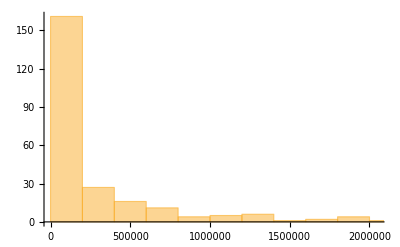

```mathematica
Histogram[{countryAreaData[[All,3]]}]
```

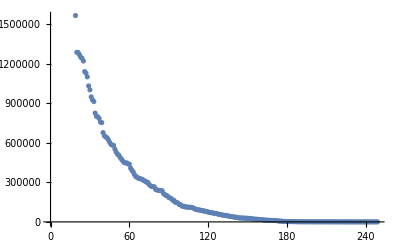

```mathematica
ListPlot[countryAreaData[[All,3]]]
```

```mathematica
WolframAlpha["population and area of countries",TimeConstraint->60]
```

WolframAlphaQueryResults

```mathematica
countryAreaPopData=WolframAlpha["population and area of countries",{{"PropertyRanking:CountryData",1},"ComputableData"}]
```

{{{,,population,total area},{1,China,1.44×10^9 people,9.597×10^6 km^2},{2,India,1.38×10^9 people,3.287×10^6 km^2},{3,United States,3.31×10^8 people,9.631×10^6 km^2},{4,Indonesia,2.74×10^8 people,1.905×10^6 km^2},{5,Pakistan,2.21×10^8 people,796100. km^2},{6,Brazil,2.13×10^8 people,8.515×10^6 km^2},{7,Nigeria,2.06×10^8 people,923800. km^2},{8,Bangladesh,1.65×10^8 people,148500. km^2},{9,Russia,1.46×10^8 people,1.71×10^7 km^2},{10,Mexico,1.29×10^8 people,1.964×10^6 km^2},{11,Japan,1.26×10^8 people,377800. km^2},{12,Ethiopia,1.15×10^8 people,1.127×10^6 km^2},{13,Philippines,1.1×10^8 people,300000. km^2},{14,Egypt,1.02×10^8 people,1.001×10^6 km^2},{15,Vietnam,9.73×10^7 people,329600. km^2},{16,Democratic Republic of the Congo,8.96×10^7 people,2.345×10^6 km^2},{17,Turkey,8.43×10^7 people,783600. km^2},{18,Iran,8.4×10^7 people,1.648×10^6 km^2},{19,Germany,8.38×10^7 people,357000. km^2},{20,Thailand,6.98×10^7 people,513100. km^2},{21,United Kingdom,6.79×10^7 people,243600. km^2},{22,France,6.53×10^7 people,551500. km^2},{23,Italy,6.05×10^7 people,301300. km^2},{24,Tanzania,5.97×10^7 people,947300. km^2},{25,South Africa,5.93×10^7 people,1.219×10^6 km^2},{26,Myanmar,5.44×10^7 people,676600. km^2},{27,Kenya,5.38×10^7 people,580400. km^2},{28,South Korea,5.13×10^7 people,98480. km^2},{29,Colombia,5.09×10^7 people,1.139×10^6 km^2},{30,Spain,4.68×10^7 people,505400. km^2},{31,Uganda,4.57×10^7 people,236000. km^2},{32,Argentina,4.52×10^7 people,2.767×10^6 km^2},{33,Algeria,4.39×10^7 people,2.382×10^6 km^2},{34,Sudan,4.38×10^7 people,1.886×10^6 km^2},{35,Ukraine,4.37×10^7 people,603600. km^2},{36,Iraq,4.02×10^7 people,437100. km^2},{37,Afghanistan,3.89×10^7 people,652200. km^2},{38,Poland,3.78×10^7 people,312700. km^2},{39,Canada,3.77×10^7 people,9.985×10^6 km^2},{40,Morocco,3.69×10^7 people,446600. km^2},{41,Saudi Arabia,3.48×10^7 people,1.961×10^6 km^2},{42,Uzbekistan,3.35×10^7 people,447400. km^2},{43,Peru,3.3×10^7 people,1.285×10^6 km^2},{44,Angola,3.29×10^7 people,1.247×10^6 km^2},{45,Malaysia,3.24×10^7 people,329800. km^2},{46,Mozambique,3.13×10^7 people,799400. km^2},{47,Ghana,3.11×10^7 people,238500. km^2},{48,Yemen,2.98×10^7 people,528000. km^2},{49,Nepal,2.91×10^7 people,147200. km^2},{50,Venezuela,2.84×10^7 people,912100. km^2},{51,Madagascar,2.77×10^7 people,587000. km^2},{52,Cameroon,2.65×10^7 people,475400. km^2},{53,Ivory Coast,2.64×10^7 people,322500. km^2},{54,North Korea,2.58×10^7 people,120500. km^2},{55,Australia,2.55×10^7 people,7.741×10^6 km^2},{56,Niger,2.42×10^7 people,1.267×10^6 km^2},{57,Taiwan,2.38×10^7 people,35980. km^2},{58,Sri Lanka,2.14×10^7 people,65610. km^2},{59,Burkina Faso,2.09×10^7 people,274200. km^2},{60,Mali,2.03×10^7 people,1.24×10^6 km^2},{61,Romania,1.92×10^7 people,238400. km^2},{62,Malawi,1.91×10^7 people,118500. km^2},{63,Chile,1.91×10^7 people,756100. km^2},{64,Kazakhstan,1.88×10^7 people,2.725×10^6 km^2},{65,Zambia,1.84×10^7 people,752600. km^2},{66,Guatemala,1.79×10^7 people,108900. km^2},{67,Ecuador,1.76×10^7 people,283600. km^2},{68,Syria,1.75×10^7 people,185200. km^2},{69,Netherlands,1.71×10^7 people,41540. km^2},{70,Senegal,1.67×10^7 people,196700. km^2},{71,Cambodia,1.67×10^7 people,181000. km^2},{72,Chad,1.64×10^7 people,1.284×10^6 km^2},{73,Somalia,1.59×10^7 people,637700. km^2},{74,Zimbabwe,1.49×10^7 people,390800. km^2},{75,Guinea,1.31×10^7 people,245900. km^2},{76,Rwanda,1.3×10^7 people,26340. km^2},{77,Benin,1.21×10^7 people,112600. km^2},{78,Burundi,1.19×10^7 people,27830. km^2},{79,Tunisia,1.18×10^7 people,163600. km^2},{80,Bolivia,1.17×10^7 people,1.099×10^6 km^2},{81,Belgium,1.16×10^7 people,30530. km^2},{82,Haiti,1.14×10^7 people,27750. km^2},{83,Cuba,1.13×10^7 people,110900. km^2},{84,South Sudan,1.12×10^7 people,644300. km^2},{85,Dominican Republic,1.08×10^7 people,48670. km^2},{86,Czech Republic,1.07×10^7 people,78870. km^2},{87,Greece,1.04×10^7 people,131900. km^2},{88,Jordan,1.02×10^7 people,89340. km^2},{89,Portugal,1.02×10^7 people,92090. km^2},{90,Azerbaijan,1.01×10^7 people,86600. km^2},{91,Sweden,1.01×10^7 people,450300. km^2},{92,Honduras,9.9×10^6 people,112100. km^2},{93,United Arab Emirates,9.89×10^6 people,83600. km^2},{94,Hungary,9.66×10^6 people,93030. km^2},{95,Tajikistan,9.54×10^6 people,143100. km^2},{96,Belarus,9.45×10^6 people,207600. km^2},{97,Austria,9.01×10^6 people,83870. km^2},{98,Papua New Guinea,8.95×10^6 people,462800. km^2},{99,Serbia,8.79×10^6 people,77470. km^2},{100,Israel,8.66×10^6 people,20770. km^2},{101,Switzerland,8.65×10^6 people,41280. km^2},{102,Togo,8.28×10^6 people,56790. km^2},{103,Sierra Leone,7.98×10^6 people,71740. km^2},{104,Hong Kong,7.5×10^6 people,1104. km^2},{105,Laos,7.28×10^6 people,236800. km^2},{106,Paraguay,7.13×10^6 people,406800. km^2},{107,Bulgaria,6.95×10^6 people,110900. km^2},{108,Libya,6.87×10^6 people,1.76×10^6 km^2},{109,Lebanon,6.83×10^6 people,10450. km^2},{110,Nicaragua,6.62×10^6 people,130400. km^2},{111,Kyrgyzstan,6.52×10^6 people,200000. km^2},{112,El Salvador,6.49×10^6 people,21040. km^2},{113,Turkmenistan,6.03×10^6 people,488100. km^2},{114,Singapore,5.85×10^6 people,697. km^2},{115,Denmark,5.79×10^6 people,43090. km^2},{116,Finland,5.54×10^6 people,338100. km^2},{117,Republic of the Congo,5.52×10^6 people,342000. km^2},{118,Slovakia,5.46×10^6 people,49040. km^2},{119,Norway,5.42×10^6 people,323800. km^2},{120,Oman,5.11×10^6 people,309500. km^2},{121,Costa Rica,5.09×10^6 people,51100. km^2},{122,Liberia,5.06×10^6 people,111400. km^2},{123,Ireland,4.94×10^6 people,70270. km^2},{124,Central African Republic,4.83×10^6 people,623000. km^2},{125,New Zealand,4.82×10^6 people,268700. km^2},{126,Mauritania,4.65×10^6 people,1.031×10^6 km^2},{127,Panama,4.31×10^6 people,75420. km^2},{128,Kuwait,4.27×10^6 people,17820. km^2},{129,Croatia,4.11×10^6 people,56590. km^2},{130,Moldova,4.03×10^6 people,33850. km^2},{131,Georgia,3.99×10^6 people,69700. km^2},{132,Eritrea,3.55×10^6 people,117600. km^2},{133,Uruguay,3.47×10^6 people,176200. km^2},{134,Bosnia and Herzegovina,3.28×10^6 people,51200. km^2},{135,Mongolia,3.28×10^6 people,1.564×10^6 km^2},{136,Armenia,2.96×10^6 people,29740. km^2},{137,Jamaica,2.96×10^6 people,10990. km^2},{138,Qatar,2.88×10^6 people,11590. km^2},{139,Albania,2.88×10^6 people,28750. km^2},{140,Puerto Rico,2.86×10^6 people,9045. km^2},{141,West Bank,2.73×10^6 people,5860. km^2},{142,Lithuania,2.72×10^6 people,65300. km^2},{143,Namibia,2.54×10^6 people,824300. km^2},{144,Gambia,2.42×10^6 people,11300. km^2},{145,Botswana,2.35×10^6 people,581700. km^2},{146,Gabon,2.23×10^6 people,267700. km^2},{147,Lesotho,2.14×10^6 people,30360. km^2},{148,North Macedonia,2.08×10^6 people,25710. km^2},{149,Slovenia,2.08×10^6 people,20270. km^2},{150,Guinea-Bissau,1.97×10^6 people,36130. km^2},{151,Latvia,1.89×10^6 people,64590. km^2},{152,Kosovo,1.86×10^6 people,10890. km^2},{153,Gaza Strip,1.76×10^6 people,360. km^2},{154,Bahrain,1.7×10^6 people,760. km^2},{155,Equatorial Guinea,1.4×10^6 people,28050. km^2},{156,Trinidad and Tobago,1.4×10^6 people,5128. km^2},{157,Estonia,1.33×10^6 people,45230. km^2},{158,East Timor,1.32×10^6 people,14870. km^2},{159,Mauritius,1.27×10^6 people,2040. km^2},{160,Cyprus,1.21×10^6 people,9251. km^2},{161,Eswatini,1.16×10^6 people,17360. km^2},{162,Djibouti,988000. people,23200. km^2},{163,Fiji,896000. people,18270. km^2},{164,Réunion,895000. people,2517. km^2},{165,Comoros,870000. people,2235. km^2},{166,Guyana,787000. people,215000. km^2},{167,Bhutan,772000. people,38390. km^2},{168,Solomon Islands,687000. people,28900. km^2},{169,Macau,649000. people,28.2 km^2},{170,Montenegro,628000. people,13810. km^2},{171,Luxembourg,626000. people,2586. km^2},{172,Western Sahara,597000. people,266000. km^2},{173,Suriname,587000. people,163800. km^2},{174,Cape Verde,556000. people,4033. km^2},{175,Maldives,541000. people,298. km^2},{176,Malta,442000. people,316. km^2},{177,Brunei,437000. people,5765. km^2},{178,Guadeloupe,400000. people,1780. km^2},{179,Belize,398000. people,22970. km^2},{180,Bahamas,393000. people,13880. km^2},{181,Martinique,375000. people,1100. km^2},{182,Iceland,341000. people,103000. km^2},{183,Vanuatu,307000. people,12190. km^2},{184,French Guiana,299000. people,91000. km^2},{185,Barbados,287000. people,430. km^2},{186,New Caledonia,285000. people,18580. km^2},{187,French Polynesia,281000. people,4167. km^2},{188,Mayotte,273000. people,374. km^2},{189,São Tomé and Príncipe,219000. people,964. km^2},{190,Samoa,198000. people,2831. km^2},{191,Saint Lucia,184000. people,616. km^2},{192,Guam,169000. people,544. km^2},{193,Curacao,164000. people,444. km^2},{194,Kiribati,119000. people,811. km^2},{195,Micronesia,115000. people,702. km^2},{196,Grenada,113000. people,344. km^2},{197,Saint Vincent and the Grenadines,111000. people,389. km^2},{198,Aruba,107000. people,180. km^2},{199,Tonga,106000. people,747. km^2},{200,United States Virgin Islands,104000. people,349. km^2},{201,Seychelles,98300. people,455. km^2},{202,Antigua and Barbuda,97900. people,442.6 km^2},{203,Jersey,95700. people,116. km^2},{204,Isle of Man,85000. people,572. km^2},{205,Andorra,77300. people,468. km^2},{206,Dominica,72000. people,751. km^2},{207,Cayman Islands,65700. people,264. km^2},{208,Guernsey,65600. people,78. km^2},{209,Bermuda,62300. people,54. km^2},{210,Marshall Islands,59200. people,181. km^2},{211,Northern Mariana Islands,57600. people,464. km^2},{212,Greenland,56800. people,2.166×10^6 km^2},{213,American Samoa,55200. people,199. km^2},{214,Saint Kitts and Nevis,53200. people,261. km^2},{215,Faroe Islands,48900. people,1393. km^2},{216,Sint Maarten,42900. people,34. km^2},{217,Monaco,39200. people,2. km^2},{218,Turks and Caicos Islands,38700. people,948. km^2},{219,Saint Martin,38700. people,53.2 km^2},{220,Liechtenstein,38100. people,160. km^2},{221,San Marino,33900. people,61. km^2},{222,Gibraltar,33700. people,6.5 km^2},{223,British Virgin Islands,30200. people,151. km^2},{224,Aland Islands,29000. people,1580. km^2},{225,Caribbean Netherlands,26200. people,328. km^2},{226,Palau,18100. people,459. km^2},{227,Cook Islands,17600. people,236. km^2},{228,Anguilla,15000. people,91. km^2},{229,Tuvalu,11800. people,26. km^2},{230,Wallis and Futuna Islands,11200. people,142. km^2},{231,Nauru,10800. people,21. km^2},{232,Saint Barthelemy,9890. people,25. km^2},{233,Saint Helena, Ascension and Tristan da Cunha,6070. people,413. km^2},{234,Saint Pierre and Miquelon,5800. people,242. km^2},{235,Montserrat,5000. people,102. km^2},{236,Falkland Islands,3480. people,12170. km^2},{237,Svalbard,2640. people,62050. km^2},{238,British Indian Ocean Territory,2500. people,54400. km^2},{239,Norfolk Island,2200. people,36. km^2},{240,Niue,1620. people,260. km^2},{241,Christmas Island,1510. people,135. km^2},{242,Tokelau,1350. people,12. km^2},{243,Vatican City,809. people,0.44 km^2},{244,Cocos Keeling Islands,550. people,14. km^2},{245,United States Minor Outlying Islands,300. people,34.2 km^2},{246,French Southern And Antarctic lands,196. people,439800. km^2},{247,Pitcairn Islands,56. people,47. km^2},{248,South Georgia and the South Sandwich Islands,30. people,3903. km^2}},2006, 2009, 2011, 2012, 2013, 2014, 2016, 2017, and 2020 estimates}

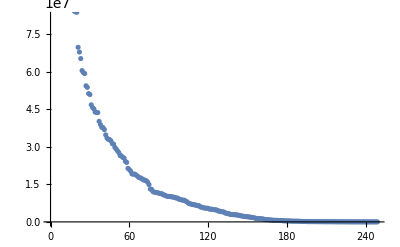

```mathematica
l1=ListPlot[countryAreaPopData[[1]][[All,3]]]
```

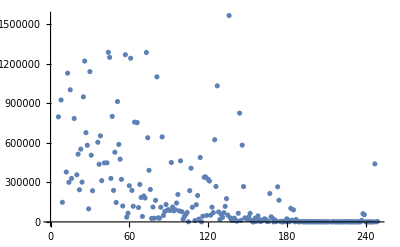

```mathematica
l2=ListPlot[countryAreaPopData[[1]][[All,4]]]
```

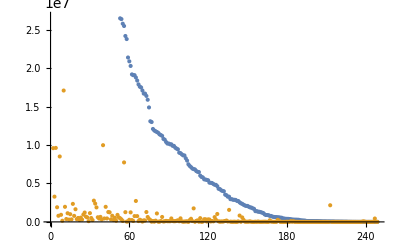

```mathematica
ListPlot[{countryAreaPopData[[1]][[All,3]],countryAreaPopData[[1]][[All,4]]}]
```

```mathematica
CloseSQLConnection[conn]
```

{}